```mathematica
By Le Chen.
Crated on Sat 30 Apr 2022 07:55:39 AM CDT
```

```mathematica
Integrate[r^(d-1)/(r^2(1+r^2)^(s/2)),{r,0,∞},Assumptions->{s>d-2,d>=3}]
```

(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2])

```mathematica
Solve[z == r^2/(1+r^2),r]
```

{{r→-(√z)/(√(1-z))},{r→(√z)/(√(1-z))}}

```mathematica
FullSimplify[(r^(d-1)/(r^2(1+r^2)^(s/2))/.r->√(z/(1-z)))D[√(z/(1-z)),z]//Expand,Assumptions->{0<z<1,s>d-2,d>=3}]
```

1/2 (1-z)^(1/2 (-d+s)) z^(-2+d/2)

```mathematica
Integrate[1/2 (1-z)^(1/2 (-d+s)) z^(-2+d/2),{z,0,1}]
```

ConditionalExpression[(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2]), Re[d-s]<2&&Re[d]>2]

```mathematica
(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2]) (2 π^(d/2))/Gamma[d/2]
```

(π^(d/2) Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(Gamma[d/2] Gamma[s/2])

```mathematica
FullSimplify[(π^(d/2) Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(Gamma[d/2] Gamma[s/2]),Assumptions->{s>d-2,d>=3}]
```

(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) Gamma[s/2])

```mathematica
(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])//TeXForm
```

\frac{2 \pi ^{d/2} \Gamma \left(\frac{1}{2} (-d+s+2)\right)}{(d-2) d \Gamma
   \left(\frac{s}{2}\right)}

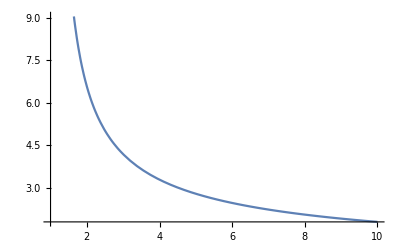

```mathematica
Plot[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])/.d->3,{s,1,10}]
```

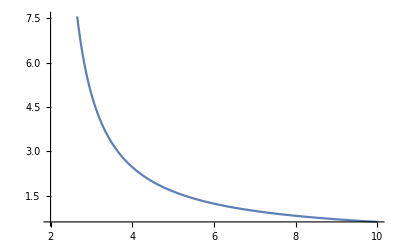

```mathematica
Plot[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])/.d->4,{s,2,10}]
```

```mathematica
Limit[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s->∞]
```

$Aborted

```mathematica
Limit[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s->∞,Assumptions->{d>=3}]
```

0

```mathematica
D[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s]//FullSimplify
```

(π^(d/2) Gamma[1/2 (2-d+s)] (-PolyGamma[0,s/2]+PolyGamma[0,1/2 (2-d+s)]))/((-2+d) d Gamma[s/2])

```mathematica
Integrate[Exp[-r z^2] z^(d+s-1),{z,1,∞},Assumptions->r>0]
```

```mathematica
Solve[D[-x √t + Log[t^(d/2+α)],t]==0,t]
```

{{t→(d+2 α)^2/x^2}}

```mathematica
FullSimplify[Exp[-x √t] t^(d/2+α)/.{t->(d+2 α)^2/x^2},Assumptions->{d≥1,α>0,x>0}]
```

ⅇ^(-d-2 α) (x/(d+2 α))^(-d-2 α)

```mathematica
Integrate[t^(α +d/2)(1+r^(2α))Exp[-√t r] r^(d-1),{r,0,∞},Assumptions->{α>0,d≥1,t>0}]
```

t^α Gamma[d]+Gamma[d+2 α]

```mathematica
Integrate[Abs[r-Abs[x]]^a 1/(√(2π))Exp[-x^2/2],{x,-∞,∞},Assumptions->{r>0,a>0}]
```

1/((1+a) √π)2^(-a/2) ⅇ^(-r^2/2) (2^(1/2+a/2) ⅇ^(r^2/2) r^(1+a) HypergeometricPFQ[{1/2,1},{1+a/2,3/2+a/2},-r^2/2]+Gamma[1+a] HypergeometricU[(1+a)/2,1/2,r^2/2]+a Gamma[1+a] HypergeometricU[(1+a)/2,1/2,r^2/2])

```mathematica
Integrate[Abs[r-Abs[x]]^a 1/(√(2π))Exp[-x^2/2],{x,r,∞},Assumptions->{r>0,a>0}]
```

(2^(-1-a/2) ⅇ^(-r^2/2) Gamma[1+a] HypergeometricU[(1+a)/2,1/2,r^2/2])/(√π)

```mathematica
Integrate[Abs[r-Abs[x]]^a 1/(√(2π))Exp[-x^2/2],{x,0,r},Assumptions->{r>0,a>0}]
```

(r^(1+a) HypergeometricPFQ[{1/2,1},{1+a/2,3/2+a/2},-r^2/2])/((1+a) √(2 π))

```mathematica
ϕ (2π)^d 2^(ν-1)/π^(d/2)Gamma[ν+d/2]/.ν->(s-d)/2//FullSimplify
```

2^(1/2 (-2+d+s)) π^(d/2) ϕ Gamma[s/2]

```mathematica
Solve[(ϕ (2π)^d 2^(ν-1)/π^(d/2)Gamma[ν+d/2]/.ν->(s-d)/2)==1,ϕ]//FullSimplify
```

{{ϕ→(2^(1-d/2-s/2) π^(-d/2))/Gamma[s/2]}}

```mathematica
Solve[D[-z^2+Log[z^(d-1)],z]==0,z]
```

{{z→-(√(-1+d))/(√2)},{z→(√(-1+d))/(√2)}}

```mathematica
FullSimplify[Exp[-z^2] z^(d-1)/.z->(√(-1+d))/(√2) ,Assumptions->{d>3}]
```

(-1+d)^(1/2 (-1+d)) (2 ⅇ)^(1/2-d/2)

```mathematica
Integrate[1/((r+z^2)^(s/2)),{z,0,∞},Assumptions->{s>1,r>0}]
```

(√π r^(1/2-s/2) Gamma[1/2 (-1+s)])/(2 Gamma[s/2])

```mathematica
Integrate[1/(r^θ(r+z^2)^(s/2)),{z,0,∞},Assumptions->{s>1,r>0,0<θ<1}]
```

(√π r^(1/2 (1-s-2 θ)) Gamma[1/2 (-1+s)])/(2 Gamma[s/2])

```mathematica
Integrate[Exp[-x^2/2] x^(d-1),{x,2r, ∞},Assumptions->{d>=3,r>0}]
```

2^(-1+d/2) Gamma[d/2,2 r^2]

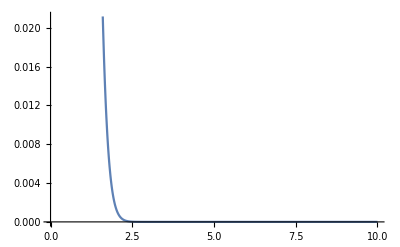

```mathematica
Plot[2^(-1+d/2) Gamma[d/2,2 r^2]/.d->3,{r,0,10}]
```

```mathematica
Limit[2^(-1+d/2) Gamma[d/2,2 r^2],r->0]
```

ConditionalExpression[2^(-1+d/2) Gamma[d/2], d>0]

```mathematica
Integrate[Exp[-x^2/2],{x,2r, ∞},Assumptions->{d>=3,r>0}]
```

√(π/2) Erfc[√2 r]

```mathematica
Integrate[t^(α+d/2)r^(2α +2d-2)Exp[-r^2 -√t r] r^(d-1),{r,0,∞},Assumptions->{t>0,d>=3,α>0}]
```

2^(2-3 d-2 α) t^(d/2+α) Gamma[-2+3 d+2 α] HypergeometricU[-1+(3 d)/2+α,1/2,t/4]

```mathematica
Integrate[(r-x)^2 Exp[-x^2/2] x^2,{x,0,∞},Assumptions->r>0]//Expand//FullSimplify
```

1/2 (3 √(2 π)+r (-8+√(2 π) r))

```mathematica
1/2 (3 √(2 π)+r (-8+√(2 π) r))//Expand//N
```

3.75994-4. r+1.25331 r^2

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,0,∞},Assumptions->{r>0,α>0}]//Expand//FullSimplify
```

(r^(1+α) HypergeometricPFQ[{1/2,1},{1+α/2,3/2+α/2},-r^2/2])/(1+α)+2^(-1-α/2) ⅇ^(-r^2/2) r Gamma[1+α] HypergeometricU[1+α/2,3/2,r^2/2]

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,r,∞},Assumptions->{r>0,α>0}]//FullSimplify
```

2^(-1-α/2) ⅇ^(-r^2/2) r Gamma[1+α] HypergeometricU[1+α/2,3/2,r^2/2]

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,0,r},Assumptions->{r>0,α>0}]//FullSimplify
```

(r^(1+α) HypergeometricPFQ[{1/2,1},{1+α/2,3/2+α/2},-r^2/2])/(1+α)

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,0,2r},Assumptions->{r>0,α>0}]//FullSimplify
```

Integrate[ⅇ^(-x^2/2) Abs[r-x]^α,{x,0,2 r},Assumptions→r>0&&α>0]

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,2r,∞},Assumptions->{r>0,α>0}]//FullSimplify
```

Integrate[ⅇ^(-x^2/2) Abs[r-x]^α,{x,2 r,∞},Assumptions→r>0&&α>0]

```mathematica
Integrate[Exp[-x^2/2],{x,2r,∞},Assumptions->{r>0,α>0}]//FullSimplify
```

√(π/2) Erfc[√2 r]

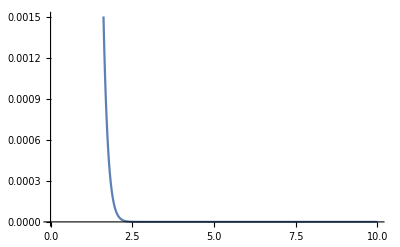

```mathematica
Plot[√(π/2) Erfc[√2 r],{r,0,10}]
```

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2]/.r->0,{x,0,∞},Assumptions->{r>0,α>0}]//FullSimplify
```

2^(1/2 (-1+α)) Gamma[(1+α)/2]